### neural network

#### Linear Layer

```mathematica
linear = NetInitialize@LinearLayer[4, "Input"->3]
```

LinearLayer[<>]

```mathematica
weights = Normal@NetExtract[linear,"Arrays"]["Weights"]
```

{{-1.07587,-0.2015,0.620672},{0.103409,0.455617,-0.503942},{-0.574429,0.700857,-0.353145},{0.163165,0.587939,-0.457212}}

```mathematica
biases=Normal@NetExtract[linear,"Arrays"]["Biases"]
```

{0.,0.,0.,0.}

```mathematica
vec={0.,0.2,.1};
linear[vec]
```

{0.0217671,0.0407291,0.104857,0.0718667}

#### setup

1 setup a function to create batches of samples

```mathematica
Batch[n_]:=Thread[#->{Plus@@#}&/@RandomInteger[10,{n,2}]]
```

```mathematica
Batch@3
```

{{2,10}→{12},{6,1}→{7},{8,5}→{13}}

2 create the data samples

```mathematica
dataT=Batch@100; 
dataV=Batch@10;
```

3 setup a net work

```mathematica
net=NetInitialize@NetChain[
{LinearLayer[{2}],LinearLayer[{1}]},
"Input"->{2},
"Output"->{1}
]
```

NetChain[<>]

```mathematica
NetExtract[net,{1,"Weights"}]//Normal
```

{{1.41237,1.6614},{-0.29996,-0.677804}}

```mathematica
net[{3,4}]
```

{2.60829}

4 train the network

```mathematica
netT=NetTrain[net,dataT,All,ValidationSet->dataV];
```

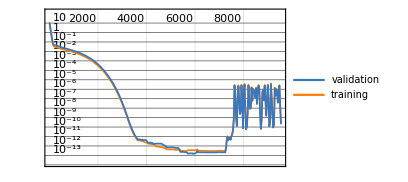
| rounds
loss | -Graphics-

```mathematica
netT["LossPlot"]
```

```mathematica
netT["RoundMeasurements"]
```

<|Loss→7.14478×10^-11|>

```mathematica
netF=netT["TrainedNet"]
```

NetChain[<>]

5 run the trained network

```mathematica
dataV[[2]]
```

{1,8}→{9}

```mathematica
dataV[[2,1]]
```

{1,8}

```mathematica
netF[dataV[[2,1]]]
```

{9.}

```mathematica
netF[{55,5.5}]
```

{60.5}

#### differentiation example

```mathematica
Batch[n_]:=Replace[
RandomReal[{-1,1},{n,1}],{
{a_/;a>0.1}:>({a}->"PLUS"),
{a_/;a<-0.1}:>({a}->"MINUS"),
{a_/;-0.1<a<0.1}:>({a}->"ZERO")
},
All
]
```

```mathematica
Batch@3
```

{{-0.982784}→MINUS,{-0.724268}→MINUS,{0.154599}→PLUS}

```mathematica
dataT=Batch@200;
dataV=Batch@20;
```

class是分类

```mathematica
net=NetInitialize@NetChain[
{
LinearLayer[6],
ElementwiseLayer[Ramp],
LinearLayer[3],
SoftmaxLayer[]
},
"Input"->{1},
"Output"->NetDecoder[{"Class",{"PLUS","MINUS","ZERO"}}]
]
```

NetChain[<>]

```mathematica
softmax = SoftmaxLayer["Input"->{3}]
```

SoftmaxLayer[<>]

```mathematica
Normal@NetExtract[net,{3,"Weights"}]
```

{{0.00965564,-0.351252,-0.0486426,-0.136555,-0.162339,0.624776},{0.176488,-0.511314,0.173666,-0.0641007,0.0316854,0.0171834},{-0.397326,0.0100224,0.162826,0.713637,0.127759,0.00949395}}

```mathematica
net[{-0.5}]
```

ZERO

```mathematica
netT=NetTrain[net,dataT,All,ValidationSet->dataV];
```

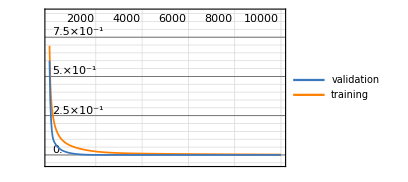
| rounds
loss | -Graphics-

<|Loss→0.00254461,ErrorRate→0.|>

NetChain[<>]

1.

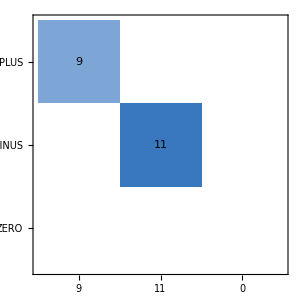
actual class | -Graphics-
 | predicted class

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
NetMeasurements[netF,dataV,"Accuracy"]
NetMeasurements[netF,dataV,"ConfusionMatrixPlot"]
```

```mathematica
netF[{-0.11},"Probabilities"]
```

<|PLUS→2.38211×10^-24,MINUS→0.974938,ZERO→0.0250618|>

#### weather forecast

四天预测第五天

```mathematica
data=WeatherData["Harbin","MeanTemperature",{{2000,1,1},{2021,12,31},"Day"}];
```

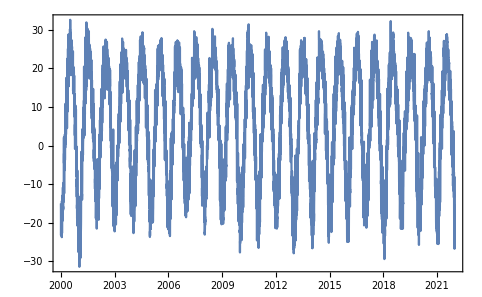

```mathematica
DateListPlot[data,Joined->True]
```

```mathematica
{date, temp}=Normal[data][[1]]
```

{Sat 1 Jan 2000 00:00:00GMT+8,-15 °C}

```mathematica
Head@temp
```

Quantity

```mathematica
data2=#[[1;;4]]->#[[5]]&/@Partition[Normal[data][[All,2,1]],5,1]
```

{{-15,-16.5,-23.22,-23.06}→-19.94,{-16.5,-23.22,-23.06,-19.94}→-21.61,{-23.22,-23.06,-19.94,-21.61}→-19.94,7972,{-23.72,-19.94,-19.83,-15.56}→-18.89,{-19.94,-19.83,-15.56,-18.89}→-22.67,{-19.83,-15.56,-18.89,-22.67}→-22.61}
 |  |  |  |

```mathematica
Partition[{1,2,3,4},3,1,1]
```

{{1,2,3},{2,3,4},{3,4,1},{4,1,2}}

```mathematica
Length@data2
```

7978

```mathematica
dataT=data2[[1;;7000]];
dataV=data2[[7001;;-1]];
```

```mathematica
net=NetInitialize@NetChain[
{
LinearLayer[{4}],
LinearLayer[{4}],
LinearLayer[{1}],
FlattenLayer[]
},
"Input"->{4},
"Output"->"Scalar"
]
```

NetChain[<>]

```mathematica
netT=NetTrain[net,dataT,All,ValidationSet->dataV];
```

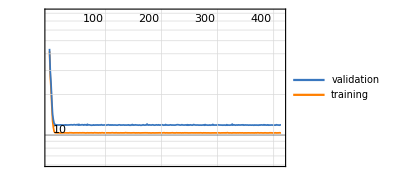
| rounds
loss | -Graphics-

<|Loss→10.3956|>

NetChain[<>]

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
```

```mathematica
n=202;
dataV[[n]]
Round[netF@dataV[[n,1]],.2]
```

{3.17,-0.17,-5.39,-4.17}→-3.06

-2.4

```mathematica
Round[netF@{3.3,5.5,4.0,4.5},.2]
```

4.6

```mathematica
data2022 = WeatherData["Harbin","MeanTemperature",{{2022,1,1},{2022,10,31},"Day"}];
```

```mathematica
dataTest=#[[1;;4]]->#[[5]]&/@Partition[Normal[data2022][[All,2,1]],5,1]
```

{{-19.78,-16.94,-18.06,-20.28}→-15.89,{-16.94,-18.06,-20.28,-15.89}→-20.06,{-18.06,-20.28,-15.89,-20.06}→-14.78,{-20.28,-15.89,-20.06,-14.78}→-20,{-15.89,-20.06,-14.78,-20}→-17.61,{-20.06,-14.78,-20,-17.61}→-19.89,{-14.78,-20,-17.61,-19.89}→-21.94,{-20,-17.61,-19.89,-21.94}→-20.89,{-17.61,-19.89,-21.94,-20.89}→-23.67,{-19.89,-21.94,-20.89,-23.67}→-16.72,{-21.94,-20.89,-23.67,-16.72}→-14.44,{-20.89,-23.67,-16.72,-14.44}→-19.61,{-23.67,-16.72,-14.44,-19.61}→-21.61,{-16.72,-14.44,-19.61,-21.61}→-21.44,{-14.44,-19.61,-21.61,-21.44}→-21.72,{-19.61,-21.61,-21.44,-21.72}→-21.33,{-21.61,-21.44,-21.72,-21.33}→-22.06,{-21.44,-21.72,-21.33,-22.06}→-18.06,{-21.72,-21.33,-22.06,-18.06}→-17.67,{-21.33,-22.06,-18.06,-17.67}→-17.11,{-22.06,-18.06,-17.67,-17.11}→-15.72,{-18.06,-17.67,-17.11,-15.72}→-15.28,{-17.67,-17.11,-15.72,-15.28}→-14.72,{-17.11,-15.72,-15.28,-14.72}→-14.44,{-15.72,-15.28,-14.72,-14.44}→-14.89,{-15.28,-14.72,-14.44,-14.89}→-15.78,{-14.72,-14.44,-14.89,-15.78}→-16.22,{-14.44,-14.89,-15.78,-16.22}→-15.22,{-14.89,-15.78,-16.22,-15.22}→-15.83,{-15.78,-16.22,-15.22,-15.83}→-16.78,{-16.22,-15.22,-15.83,-16.78}→-18.61,{-15.22,-15.83,-16.78,-18.61}→-17.56,{-15.83,-16.78,-18.61,-17.56}→-13.72,{-16.78,-18.61,-17.56,-13.72}→-11.61,{-18.61,-17.56,-13.72,-11.61}→-12.78,{-17.56,-13.72,-11.61,-12.78}→-9.5,{-13.72,-11.61,-12.78,-9.5}→-10.94,{-11.61,-12.78,-9.5,-10.94}→-12.44,{-12.78,-9.5,-10.94,-12.44}→-17.28,{-9.5,-10.94,-12.44,-17.28}→-19.5,{-10.94,-12.44,-17.28,-19.5}→-18.11,{-12.44,-17.28,-19.5,-18.11}→-17.28,{-17.28,-19.5,-18.11,-17.28}→-14.78,{-19.5,-18.11,-17.28,-14.78}→-15.78,{-18.11,-17.28,-14.78,-15.78}→-13,{-17.28,-14.78,-15.78,-13}→-16.28,{-14.78,-15.78,-13,-16.28}→-17.44,{-15.78,-13,-16.28,-17.44}→-17.72,{-13,-16.28,-17.44,-17.72}→-17.22,{-16.28,-17.44,-17.72,-17.22}→-11.28,{-17.44,-17.72,-17.22,-11.28}→-6.89,{-17.72,-17.22,-11.28,-6.89}→-3,{-17.22,-11.28,-6.89,-3}→-5.56,{-11.28,-6.89,-3,-5.56}→-5.61,{-6.89,-3,-5.56,-5.61}→-4,{-3,-5.56,-5.61,-4}→-4,{-5.56,-5.61,-4,-4}→-6.94,{-5.61,-4,-4,-6.94}→-2.56,{-4,-4,-6.94,-2.56}→-2,{-4,-6.94,-2.56,-2}→-6.61,{-6.94,-2.56,-2,-6.61}→-7.83,{-2.56,-2,-6.61,-7.83}→-4.83,{-2,-6.61,-7.83,-4.83}→-1.33,{-6.61,-7.83,-4.83,-1.33}→4.11,{-7.83,-4.83,-1.33,4.11}→3.72,{-4.83,-1.33,4.11,3.72}→0.72,{-1.33,4.11,3.72,0.72}→1,{4.11,3.72,0.72,1}→-1.22,{3.72,0.72,1,-1.22}→-2.94,{0.72,1,-1.22,-2.94}→-0.67,{1,-1.22,-2.94,-0.67}→-4.94,{-1.22,-2.94,-0.67,-4.94}→-7.56,{-2.94,-0.67,-4.94,-7.56}→-5.11,{-0.67,-4.94,-7.56,-5.11}→-4.5,{-4.94,-7.56,-5.11,-4.5}→-2.06,{-7.56,-5.11,-4.5,-2.06}→-1.78,{-5.11,-4.5,-2.06,-1.78}→2.5,{-4.5,-2.06,-1.78,2.5}→2.89,{-2.06,-1.78,2.5,2.89}→3.94,{-1.78,2.5,2.89,3.94}→2.83,{2.5,2.89,3.94,2.83}→1.5,{2.89,3.94,2.83,1.5}→2.28,{3.94,2.83,1.5,2.28}→8.39,{2.83,1.5,2.28,8.39}→1.28,{1.5,2.28,8.39,1.28}→0.89,{2.28,8.39,1.28,0.89}→1,{8.39,1.28,0.89,1}→3.06,{1.28,0.89,1,3.06}→7.22,{0.89,1,3.06,7.22}→12.61,{1,3.06,7.22,12.61}→13.33,{3.06,7.22,12.61,13.33}→0.39,{7.22,12.61,13.33,0.39}→1.17,{12.61,13.33,0.39,1.17}→4.11,{13.33,0.39,1.17,4.11}→7.83,{0.39,1.17,4.11,7.83}→9.33,{1.17,4.11,7.83,9.33}→12.94,{4.11,7.83,9.33,12.94}→5.17,{7.83,9.33,12.94,5.17}→5.72,{9.33,12.94,5.17,5.72}→7.17,{12.94,5.17,5.72,7.17}→6.06,{5.17,5.72,7.17,6.06}→8.89,{5.72,7.17,6.06,8.89}→7,{7.17,6.06,8.89,7}→5.33,{6.06,8.89,7,5.33}→11.33,{8.89,7,5.33,11.33}→19,{7,5.33,11.33,19}→20.94,{5.33,11.33,19,20.94}→9.06,{11.33,19,20.94,9.06}→9.67,{19,20.94,9.06,9.67}→13.33,{20.94,9.06,9.67,13.33}→10.61,{9.06,9.67,13.33,10.61}→15.94,{9.67,13.33,10.61,15.94}→6.44,{13.33,10.61,15.94,6.44}→7.28,{10.61,15.94,6.44,7.28}→9.28,{15.94,6.44,7.28,9.28}→11.78,{6.44,7.28,9.28,11.78}→5.44,{7.28,9.28,11.78,5.44}→5.83,{9.28,11.78,5.44,5.83}→11.22,{11.78,5.44,5.83,11.22}→15.72,{5.44,5.83,11.22,15.72}→23.11,{5.83,11.22,15.72,23.11}→17.44,{11.22,15.72,23.11,17.44}→6.94,{15.72,23.11,17.44,6.94}→11.28,{23.11,17.44,6.94,11.28}→19.83,{17.44,6.94,11.28,19.83}→18.78,{6.94,11.28,19.83,18.78}→9.72,{11.28,19.83,18.78,9.72}→11.44,{19.83,18.78,9.72,11.44}→10.5,{18.78,9.72,11.44,10.5}→11.5,{9.72,11.44,10.5,11.5}→13.44,{11.44,10.5,11.5,13.44}→14.28,{10.5,11.5,13.44,14.28}→17.72,{11.5,13.44,14.28,17.72}→18.78,{13.44,14.28,17.72,18.78}→17.44,{14.28,17.72,18.78,17.44}→22.67,{17.72,18.78,17.44,22.67}→17.56,{18.78,17.44,22.67,17.56}→20.17,{17.44,22.67,17.56,20.17}→23.83,{22.67,17.56,20.17,23.83}→15,{17.56,20.17,23.83,15}→11.67,{20.17,23.83,15,11.67}→13.5,{23.83,15,11.67,13.5}→15.83,{15,11.67,13.5,15.83}→18.28,{11.67,13.5,15.83,18.28}→16.06,{13.5,15.83,18.28,16.06}→13.39,{15.83,18.28,16.06,13.39}→16.06,{18.28,16.06,13.39,16.06}→15.33,{16.06,13.39,16.06,15.33}→19.33,{13.39,16.06,15.33,19.33}→19.33,{16.06,15.33,19.33,19.33}→18.17,{15.33,19.33,19.33,18.17}→11.72,{19.33,19.33,18.17,11.72}→12.61,{19.33,18.17,11.72,12.61}→17.5,{18.17,11.72,12.61,17.5}→20.67,{11.72,12.61,17.5,20.67}→20.22,{12.61,17.5,20.67,20.22}→19.83,{17.5,20.67,20.22,19.83}→20.83,{20.67,20.22,19.83,20.83}→21.83,{20.22,19.83,20.83,21.83}→19.61,{19.83,20.83,21.83,19.61}→20.28,{20.83,21.83,19.61,20.28}→20.56,{21.83,19.61,20.28,20.56}→17.94,{19.61,20.28,20.56,17.94}→20.78,{20.28,20.56,17.94,20.78}→21.83,{20.56,17.94,20.78,21.83}→24.11,{17.94,20.78,21.83,24.11}→26.56,{20.78,21.83,24.11,26.56}→25.94,{21.83,24.11,26.56,25.94}→25.44,{24.11,26.56,25.94,25.44}→23.06,{26.56,25.94,25.44,23.06}→20.17,{25.94,25.44,23.06,20.17}→20.89,{25.44,23.06,20.17,20.89}→23.11,{23.06,20.17,20.89,23.11}→25.89,{20.17,20.89,23.11,25.89}→23.72,{20.89,23.11,25.89,23.72}→23.67,{23.11,25.89,23.72,23.67}→25.17,{25.89,23.72,23.67,25.17}→25.89,{23.72,23.67,25.17,25.89}→24.61,{23.67,25.17,25.89,24.61}→26.11,{25.17,25.89,24.61,26.11}→24.83,{25.89,24.61,26.11,24.83}→25.5,{24.61,26.11,24.83,25.5}→26.94,{26.11,24.83,25.5,26.94}→23.67,{24.83,25.5,26.94,23.67}→25.39,{25.5,26.94,23.67,25.39}→23.89,{26.94,23.67,25.39,23.89}→24.56,{23.67,25.39,23.89,24.56}→24.06,{25.39,23.89,24.56,24.06}→25.56,{23.89,24.56,24.06,25.56}→24.17,{24.56,24.06,25.56,24.17}→21.44,{24.06,25.56,24.17,21.44}→22.5,{25.56,24.17,21.44,22.5}→22.72,{24.17,21.44,22.5,22.72}→23.39,{21.44,22.5,22.72,23.39}→22.72,{22.5,22.72,23.39,22.72}→24,{22.72,23.39,22.72,24}→25.5,{23.39,22.72,24,25.5}→26.33,{22.72,24,25.5,26.33}→25.44,{24,25.5,26.33,25.44}→23.94,{25.5,26.33,25.44,23.94}→22.17,{26.33,25.44,23.94,22.17}→24,{25.44,23.94,22.17,24}→26.28,{23.94,22.17,24,26.28}→27.94,{22.17,24,26.28,27.94}→27,{24,26.28,27.94,27}→23.11,{26.28,27.94,27,23.11}→23.94,{27.94,27,23.11,23.94}→26.89,{27,23.11,23.94,26.89}→26.44,{23.11,23.94,26.89,26.44}→28.28,{23.94,26.89,26.44,28.28}→29.5,{26.89,26.44,28.28,29.5}→28.11,{26.44,28.28,29.5,28.11}→24.78,{28.28,29.5,28.11,24.78}→25.67,{29.5,28.11,24.78,25.67}→22.11,{28.11,24.78,25.67,22.11}→20.78,{24.78,25.67,22.11,20.78}→24.28,{25.67,22.11,20.78,24.28}→24.44,{22.11,20.78,24.28,24.44}→20,{20.78,24.28,24.44,20}→20.56,{24.28,24.44,20,20.56}→19.28,{24.44,20,20.56,19.28}→21.17,{20,20.56,19.28,21.17}→22,{20.56,19.28,21.17,22}→22.22,{19.28,21.17,22,22.22}→23.56,{21.17,22,22.22,23.56}→24,{22,22.22,23.56,24}→18.5,{22.22,23.56,24,18.5}→19.06,{23.56,24,18.5,19.06}→19.22,{24,18.5,19.06,19.22}→15,{18.5,19.06,19.22,15}→17.5,{19.06,19.22,15,17.5}→18.5,{19.22,15,17.5,18.5}→15.56,{15,17.5,18.5,15.56}→15.33,{17.5,18.5,15.56,15.33}→16.89,{18.5,15.56,15.33,16.89}→20,{15.56,15.33,16.89,20}→16.72,{15.33,16.89,20,16.72}→18.28,{16.89,20,16.72,18.28}→18.44,{20,16.72,18.28,18.44}→16.17,{16.72,18.28,18.44,16.17}→20.22,{18.28,18.44,16.17,20.22}→20.94,{18.44,16.17,20.22,20.94}→18.67,{16.17,20.22,20.94,18.67}→15.22,{20.22,20.94,18.67,15.22}→14.61,{20.94,18.67,15.22,14.61}→17.72,{18.67,15.22,14.61,17.72}→20,{15.22,14.61,17.72,20}→19,{14.61,17.72,20,19}→21.83,{17.72,20,19,21.83}→21.78,{20,19,21.83,21.78}→20.17,{19,21.83,21.78,20.17}→14.44,{21.83,21.78,20.17,14.44}→17.94,{21.78,20.17,14.44,17.94}→18.61,{20.17,14.44,17.94,18.61}→17.83,{14.44,17.94,18.61,17.83}→17.28,{17.94,18.61,17.83,17.28}→13.39,{18.61,17.83,17.28,13.39}→7.67,{17.83,17.28,13.39,7.67}→11.22,{17.28,13.39,7.67,11.22}→18.67,{13.39,7.67,11.22,18.67}→17.28,{7.67,11.22,18.67,17.28}→13.22,{11.22,18.67,17.28,13.22}→13.72,{18.67,17.28,13.22,13.72}→17.94,{17.28,13.22,13.72,17.94}→12.06,{13.22,13.72,17.94,12.06}→20.33,{13.72,17.94,12.06,20.33}→15.56,{17.94,12.06,20.33,15.56}→18.94,{12.06,20.33,15.56,18.94}→15.67,{20.33,15.56,18.94,15.67}→8.89,{15.56,18.94,15.67,8.89}→14.17,{18.94,15.67,8.89,14.17}→4.22,{15.67,8.89,14.17,4.22}→3.28,{8.89,14.17,4.22,3.28}→3.28,{14.17,4.22,3.28,3.28}→5.67,{4.22,3.28,3.28,5.67}→5.89,{3.28,3.28,5.67,5.89}→7.5,{3.28,5.67,5.89,7.5}→5.89,{5.67,5.89,7.5,5.89}→5.89,{5.89,7.5,5.89,5.89}→7.67,{7.5,5.89,5.89,7.67}→12.78,{5.89,5.89,7.67,12.78}→9.83,{5.89,7.67,12.78,9.83}→11.17,{7.67,12.78,9.83,11.17}→9.78,{12.78,9.83,11.17,9.78}→5.83,{9.83,11.17,9.78,5.83}→2.78,{11.17,9.78,5.83,2.78}→2.83,{9.78,5.83,2.78,2.83}→9.33,{5.83,2.78,2.83,9.33}→11.83,{2.78,2.83,9.33,11.83}→7.11,{2.83,9.33,11.83,7.11}→5.44,{9.33,11.83,7.11,5.44}→2.28,{11.83,7.11,5.44,2.28}→1.94,{7.11,5.44,2.28,1.94}→11.83,{5.44,2.28,1.94,11.83}→4.5,{2.28,1.94,11.83,4.5}→0.39,{1.94,11.83,4.5,0.39}→0.22,{11.83,4.5,0.39,0.22}→1.33,{4.5,0.39,0.22,1.33}→6.56,{0.39,0.22,1.33,6.56}→5.94}

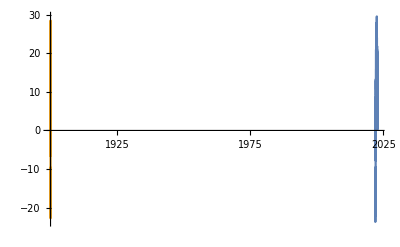

```mathematica
ListLinePlot[{data2022,netF@dataTest[[All,1]]}]
```

#### grid data from weather stations

```mathematica
data=CloudGet@CloudObject["https://www.wolframcloud.com/obj/31898187-89a9-4b86-b5e6-ab36d63de789"];
```

```mathematica
data[[1]]
```

{-0.94,1.56,-3.22,2.56,-11.11,3.33,-0.67,2.89,1.94,3.22,3,3.56,2.61,0.33,2.17,2.67,2.67,2.67,0.5,3.11,2.94,2.17,0.5,0.5,1.17,-7.33,-0.72,-10.06,2.44,-20.78,-1.44,-9.44,-1.22,-2.67,-0.5,-1.5,-1.44,-2.44,-7.28,-4.39,-1.11,-2.44,-2.44,-6.5,-1.89,0.17,-0.33,-6.5,-6.5,-3.22,-9.17,-4.44,-10.61,-3.39,-20.72,-5.28,-8,-5.83,-7.56,-4.44,-3.28,-4.94,-4.33,-7.56,-6.39,-3.06,-5.5,-5.5,-7,-4.94,-0.72,-0.22,-7,-7,-5.11,-6.17,-2.44,-11.72,-3.78,-14.89,-4,-5.94,-2.72,-5.5,-3.11,-5,-6.28,-6,-6.33,-7.56,-4.83,-7.94,-7.94,-7.39,-5.89,-2.56,-2.94,-7.39,-7.39,-7.78}→{-3.78,-3.28,-10,-2.89,-13.33,-3.33,-3.44,-1.67,-5.61,-3.44,-3.94,-4.89,-5.89,-4.78,-7.33,-4.17,-6.39,-6.39,-9.06,-5.06,-3.72,-4.39,-9.06,-9.06,-7.56}

```mathematica
data4=Cases[data,(a_->b_):>(a->b[[13]]),1];
```

```mathematica
data4[[1]]
```

{-0.94,1.56,-3.22,2.56,-11.11,3.33,-0.67,2.89,1.94,3.22,3,3.56,2.61,0.33,2.17,2.67,2.67,2.67,0.5,3.11,2.94,2.17,0.5,0.5,1.17,-7.33,-0.72,-10.06,2.44,-20.78,-1.44,-9.44,-1.22,-2.67,-0.5,-1.5,-1.44,-2.44,-7.28,-4.39,-1.11,-2.44,-2.44,-6.5,-1.89,0.17,-0.33,-6.5,-6.5,-3.22,-9.17,-4.44,-10.61,-3.39,-20.72,-5.28,-8,-5.83,-7.56,-4.44,-3.28,-4.94,-4.33,-7.56,-6.39,-3.06,-5.5,-5.5,-7,-4.94,-0.72,-0.22,-7,-7,-5.11,-6.17,-2.44,-11.72,-3.78,-14.89,-4,-5.94,-2.72,-5.5,-3.11,-5,-6.28,-6,-6.33,-7.56,-4.83,-7.94,-7.94,-7.39,-5.89,-2.56,-2.94,-7.39,-7.39,-7.78}→-5.89

```mathematica
dataT2=data4[[1;;3650]];
dataV2=data4[[3651;;-1]];
```

```mathematica
net2=NetInitialize@NetChain[
{
LinearLayer[{50}],
LinearLayer[{20}],
LinearLayer[{1}],
FlattenLayer[]
},
"Input"->{100},
"Output"->"Scalar"
]
```

NetChain[<>]

```mathematica
netT2=NetTrain[net2,dataT2,All,ValidationSet->dataV2];
```

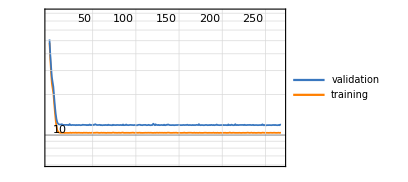
| rounds
loss | -Graphics-

<|Loss→10.3907|>

NetChain[<>]

```mathematica
netT3=NetTrain[net,dataT,All,ValidationSet->dataV];
netT3["LossPlot"]
netT3["RoundMeasurements"]
netF3=netT3["TrainedNet"]
```

#### discontinuity problem

```mathematica
Batch[n_]:=Thread[#->If[#[[1]]>5,Plus@@#,Subtract@@#]&/@RandomInteger[10,{n,2}]]
```

```mathematica
Batch[10]
```

{{1,3}→-2,{0,2}→-2,{7,4}→11,{1,2}→-1,{3,10}→-7,{0,4}→-4,{9,10}→19,{3,4}→-1,{3,4}→-1,{0,1}→-1}

```mathematica
ListPlot3D[Cases[Batch[1000],(a_->b_):>Append[a,b],All]]
```

-Graphics3D-

```mathematica
dataT=Batch@1000;
dataV=Batch@100;
```

区别：ramp

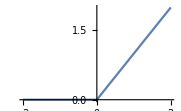

```mathematica
Plot[Ramp[x],{x,-2,2}]
```

```mathematica
net1=NetInitialize@NetChain[{LinearLayer[{12}],LinearLayer[{12}],LinearLayer[{1}],FlattenLayer[]},"Input"->{2},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
net2=NetInitialize@NetChain[{LinearLayer[{12}],Ramp,LinearLayer[{12}],LinearLayer[{1}],FlattenLayer[]},"Input"->{2},"Output"->"Scalar"]
```

NetChain[<>]

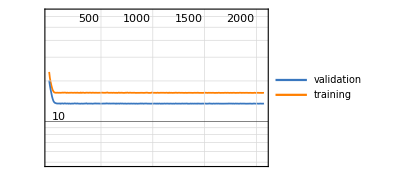
| rounds
loss | -Graphics-

<|Loss→16.2784|>

NetChain[<>]

```mathematica
netT1=NetTrain[net1,dataT,All,ValidationSet->dataV];
netT1["LossPlot"]
netT1["RoundMeasurements"]
netF1=netT1["TrainedNet"]
```

```mathematica
ListPlot3D[Cases[dataV,(a_->b_):>Append[a,netF1@a],All]]
```

-Graphics3D-

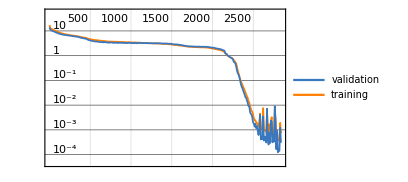
| rounds
loss | -Graphics-

<|Loss→0.000609729|>

NetChain[<>]

23.3536

```mathematica
netT2=NetTrain[net2,dataT,All,ValidationSet->dataV];
netT2["LossPlot"]
netT2["RoundMeasurements"]
netF2=netT2["TrainedNet"]
netT2["TotalTrainingTime"]
```

```mathematica
ListPlot3D[Cases[Batch@1000,(a_->b_):>Append[a,netF2@a],All]]
```

-Graphics3D-

#### localization problem

```mathematica
data={{7.5,1}->0,{11,1}->1,{12,1}->0,{18,1}->1,{13,2}->0,{3,3}->0,{6,3}->0,{7,3}->0,{8.5,3}->1,{11,3}->0,{3,4}->0,{7,4}->0,{8.5,4}->0,{10,4}->0,{5,5}->0,{7,5}->0,{8,5}->0,{10,5}->1,{11,5}->1,{16,5}->1,{6,6}->1,{9,6}->1,{10,6}->0,{3,7}->0,{5,7}->0,{8,7}->1,{15,7}->1,{20,7}->1,{3,8}->0,{4,8}->0,{8,8}->0,{12,8}->0,{16,8}->1};
```

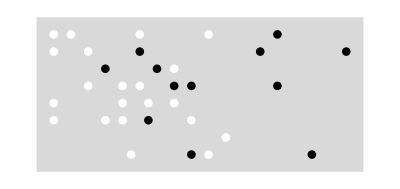

```mathematica
Graphics[{{LightGray,Rectangle[{2,0},{21,9}]},Replace[data,(a_->b_):>{GrayLevel[1-b],Disk[a,.25]},All]}]
```

```mathematica
net1=NetInitialize@NetChain[{LinearLayer[{4}],LinearLayer[{2}],SoftmaxLayer[]},"Input"->{2},"Output"->NetDecoder[{"Class",{0,1}}]]
```

NetChain[<>]

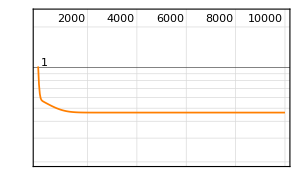
| rounds
loss | -Graphics-

<|Loss→0.46391,ErrorRate→0.242424|>

NetChain[<>]

```mathematica
netT1=NetTrain[net1,data,All];
netT1["LossPlot"]
netT1["RoundMeasurements"]
netF1=netT1["TrainedNet"]
```

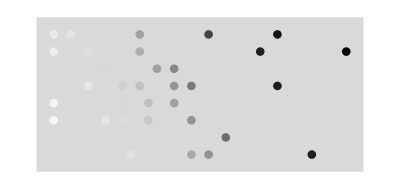

```mathematica
Graphics[{{LightGray,Rectangle[{2,0},{21,9}]},Cases[data,(a_->b_):>{GrayLevel@netF1[a,"Probabilities"][0],Disk[a,.25]},All]}]
```

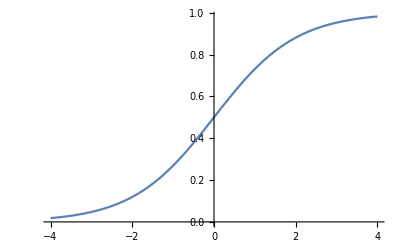

```mathematica
Plot[LogisticSigmoid[x],{x,-4,4}]
```

```mathematica
net2=NetInitialize@NetChain[
{
LinearLayer[{4}],
LogisticSigmoid,
LinearLayer[{2}],
SoftmaxLayer[]
},
"Input"->{2},
"Output"->NetDecoder[{"Class",{0,1}}]
]
```

NetChain[<>]

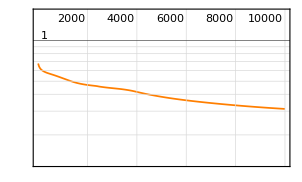
| rounds
loss | -Graphics-

<|Loss→0.31157,ErrorRate→0.242424|>

NetChain[<>]

```mathematica
netT2=NetTrain[net2,data,All];
netT2["LossPlot"]
netT2["RoundMeasurements"]
netF2=netT2["TrainedNet"]
```

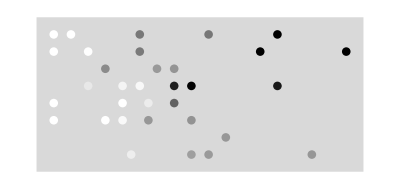

```mathematica
Graphics[{{LightGray,Rectangle[{2,0},{21,9}]},Cases[data,(a_->b_):>{GrayLevel@netF2[a,"Probabilities"][0],Disk[a,.25]},All]}]
```

non - linear optimization

```mathematica
net3=NetInitialize@NetChain[
{
LinearLayer[{8}],
LogisticSigmoid,
LinearLayer[{8}],
LinearLayer[{2}],
SoftmaxLayer[]
},
"Input"->{2},
"Output"->NetDecoder[{"Class",{0,1}}]
]
```

NetChain[<>]

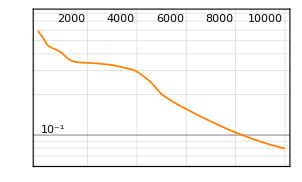
| rounds
loss | -Graphics-

<|Loss→0.0793025,ErrorRate→0.0606061|>

NetChain[<>]

```mathematica
netT3=NetTrain[net3,data,All];
netT3["LossPlot"]
netT3["RoundMeasurements"]
netF3=netT3["TrainedNet"]
```

NetChain[<>]

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:6885  rounds:6884  time:5.1s  examples/s:44228
data | ,,  training examples:33  processed examples:227205  skipped examples:0
method | ,,  ADAMoptimizer  batch size33CPU
round | ,,  loss:4.64×10^-1  error:24.2%
 | 
 | ]

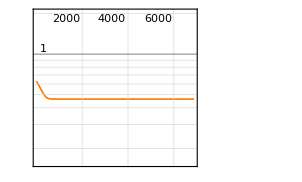
| rounds
loss | -Graphics-

<|Loss→0.46391,ErrorRate→0.242424|>

NetChain[<>]

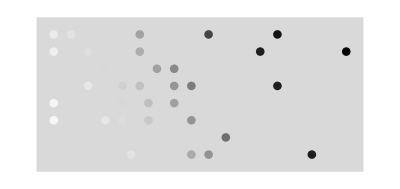

```mathematica
net4=NetInitialize@NetChain[{LinearLayer[{8}],LinearLayer[{8}],LinearLayer[{2}],SoftmaxLayer[]},"Input"->{2},"Output"->NetDecoder[{"Class",{0,1}}]]

netT4=NetTrain[net4,data,All]
netT4["LossPlot"]
netT4["RoundMeasurements"]
netF4=netT4["TrainedNet"]

Graphics[{{LightGray,Rectangle[{2,0},{21,9}]},Cases[data,(a_->b_):>{GrayLevel@netF4[a,"Probabilities"][0],Disk[a,.25]},All]}]
```